```mathematica
SetDirectory[NotebookDirectory[]];
```

## 杂七杂八

1.20185

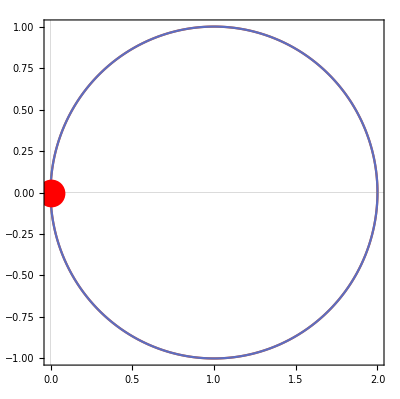

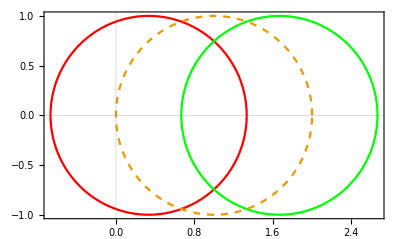

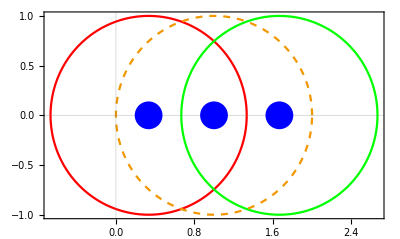

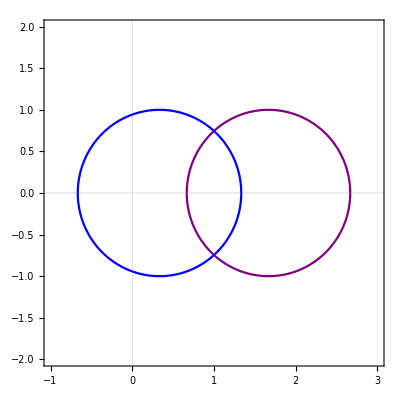

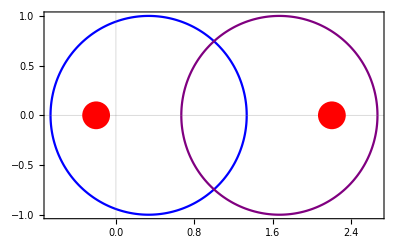

```mathematica
{t1=1.,t2=1.0,gam=4/3,t3=0.0};
points={{√(t2^2+(gam/2)^2)+t1,0},{-√(t2^2+(gam/2)^2)+t1,0}};
oir=Graphics[{Red,PointSize[0.05],Point[{0,0}]}];
circle={{t1,0},{t1+gam/2,0},{t1-gam/2,0}};
phasePoint=√(t2^2+(gam/2)^2)
cirPoints=Graphics[{Blue,PointSize[0.05],Point[circle]}];
hermitian=ParametricPlot[{{t1+t2 Cos[k],t2 Sin[k]},{t1+t2 Cos[k],-t2 Sin[k]}},{k,0,2Pi},PlotTheme->"Scientific",FrameStyle->Directive[24,Bold]];
Show[{hermitian,oir}]
coll=ParametricPlot[{{t1+t2 Cos[k]-gam/2,t2 Sin[k]},{t1+t2 Cos[k]+gam/2,-t2 Sin[k]},{t1+t2 Cos[k],t2 Sin[k]}},{k,0,2Pi},PlotTheme->"Scientific",FrameStyle->Directive[24,Bold],PlotStyle->{Red,Green,Dashed}]
Show[{coll,cirPoints}]
nonHermitian=ParametricPlot[{{t1+t2 Cos[k]-gam/2,t2 Sin[k]},{t1+t2 Cos[k]+gam/2,-t2 Sin[k]}},{k,0,2Pi},PlotTheme->"Scientific",FrameStyle->Directive[24,Bold],PlotStyle->{Blue,Purple},PlotRange->{{-1,3},{-2,2}}]
pt=Graphics[{Red,PointSize[0.05],Point[points]}];
Show[{nonHermitian,pt},PlotRange->All]
```

## 能带图

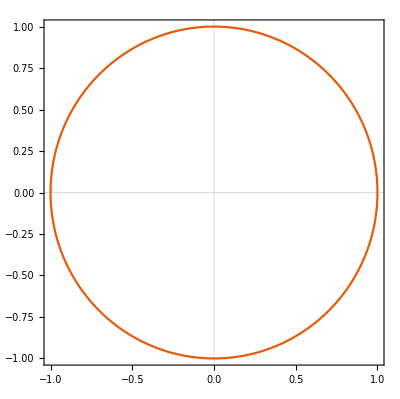

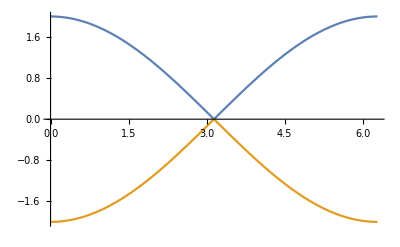

```mathematica
{t1=1.0,t2=1.0,gam=4/3,t3=0.0};
eng[k_]:=√((t1+t2 Cos[k])^2+(t2 Sin[k])^2)
ParametricPlot[{Cos[k],Sin[k]},{k,0,2Pi},PlotTheme->"Scientific"]
Plot[{eng[k],-eng[k]},{k,0,2Pi}]
```

## 厄密Winding

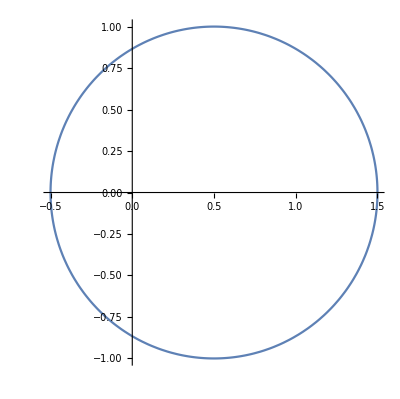

```mathematica
{t1=0.5,t2=1.0,gam=4/3,t3=0.0};(*厄密情况下看dx和dy构成的参数对原点的Winding*)
ParametricPlot[{t1+t2 Cos[k],t2 Sin[k]},{k,0,2Pi}]
```

## 非厄密Winding

1.20185

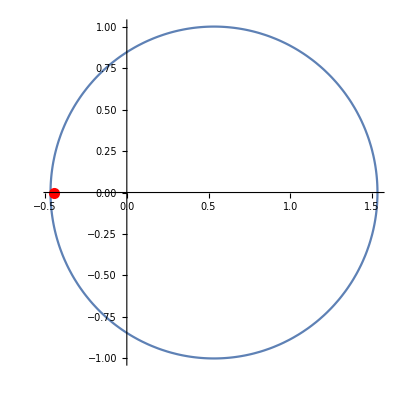

```mathematica
{t1=1.2,t2=1.0,gam=4/3,t3=0.0};(**)
origin=Graphics[{Red,PointSize[0.02],Point[{-(gam/2)^2,0}]}];(*gam导致的圆心平移*)
phasePoint=√(t2^2+(gam/2)^2)(*非厄密预言t1的相变点*)
loop=ParametricPlot[{t1+t2 Cos[k]-gam/2.0,t2 Sin[k]},{k,0,2Pi}];
Show[{loop,origin},PlotRange->All]
```

## Wind 示意图

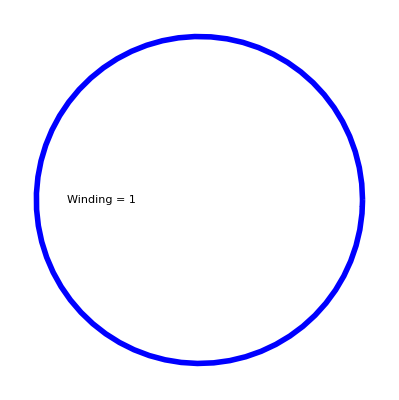

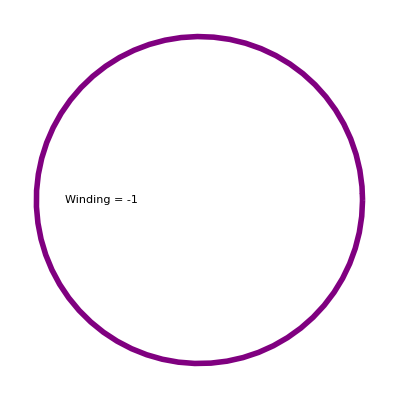

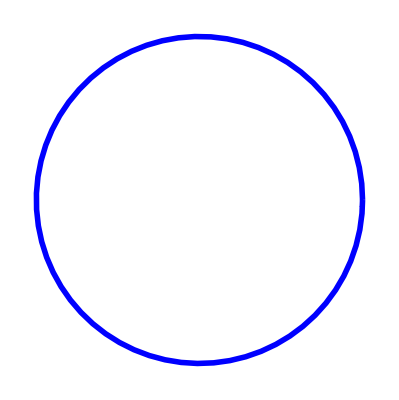

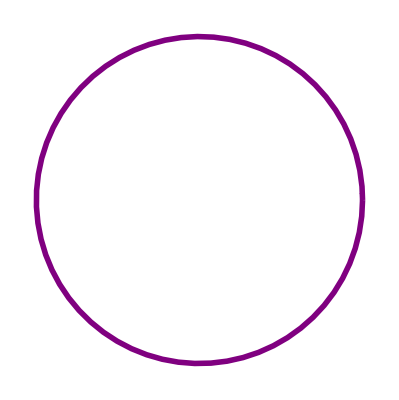

```mathematica
{t1=0.6,t2=1.0,gam=0,t3=0.0,dk=0.1};
pt1[k_]:={t1+t2 Cos[k],t2 Sin[k]}
pt2[k_]:={t1+t2 Cos[k],-t2 Sin[k]}
ar1[ϕ_]:={{0,0},pt1[ϕ]}
ar2[ϕ_]:={{0,0},pt2[ϕ]}
arp1=Table[ar1[ϕ],{ϕ,0,2Pi,dk}];
ro1=Table[pt1[ϕ],{ϕ,0,2Pi,dk}]/.{p1_,pn___}:>{p1,pn,p1};(*最后利用模式匹配将首尾连接起来*)
ro2=Table[pt2[ϕ],{ϕ,0,2Pi,dk}]/.{p1_,pn___}:>{p1,pn,p1};
arp2=Table[ar2[ϕ],{ϕ,0,2Pi,dk}];
line1=Line[ro1];
wind1=WindingCount[line1,{0,0}];
wind2=WindingCount[line2,{0,0}];
line2=Line[ro2];
vor1=Graphics[{{Blue,Arrowheads[0.2],Thickness[0.01],Arrow[ro1]},{Text[Style[StringJoin["Winding = ",ToString@wind1],Large],{0,0}]}}]

vor2=Graphics[{{Purple,Thickness[0.01],Arrowheads[0.2],Arrow[ro2]},{Text[Style[StringJoin["Winding = ",ToString@wind2],Large],{0,0}]}}]
vor1=Graphics[{{Blue,Arrowheads[0.2],Thickness[0.01],Arrow[ro1]}}]

vor2=Graphics[{{Purple,Thickness[0.01],Arrowheads[0.2],Arrow[ro2]}}]
```

## 切线求解

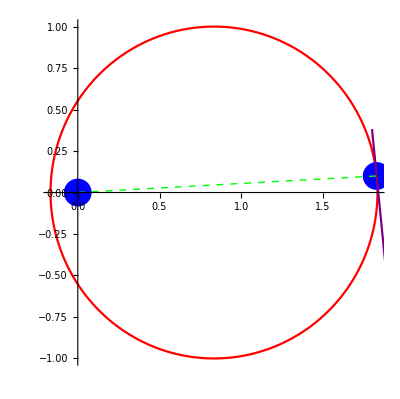

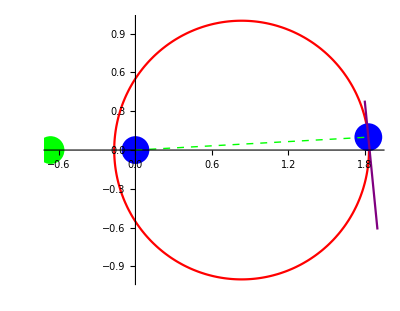

```mathematica
{t1=1.5,t2=1.0,gam=4/3,t3=0.0};
shift1[k_]:={t1+t2 Cos[k]-gam/2,t2 Sin[k]}
shift2[k_]:={t1+t2 Cos[k]+gam/2,t2 Sin[k]}
tan1[k_]:=Module[{x,val},val=D[shift1[x],x]/.{x->k};val[[2]]/val[[1]]](*计算参数图上每一点的切线斜率,符号计算*)
tan2[k_]:=Module[{x,val},val=D[shift2[x],x]/.{x->k};val[[2]]/val[[1]]]
coll=ParametricPlot[{{t1+t2 Cos[k]-gam/2,t2 Sin[k]},{t1+t2 Cos[k]+gam/2,-t2 Sin[k]},{t1+t2 Cos[k],t2 Sin[k]}},{k,0,2Pi},PlotTheme->"Scientific",FrameStyle->Directive[24,Bold],PlotStyle->{Red,Green,Dashed}];
k=0.1;(*点在参数坐标上的转角*)
circle=ParametricPlot[{t1+t2 Cos[k]-gam/2,t2 Sin[k]},{k,0,2Pi},PlotStyle->Red];(*绘制参数圆*)
point=Graphics[{Blue,PointSize[0.05],Point[{{0,0},shift1[k]}]}];
shiftPoint=Graphics[{Green,PointSize[0.05],Point[{-gam/2,0}]}];
line=Graphics[{Green,Dashed,Thick,Line[{{0,0},shift1[k]}]}];
line1=Plot[tan1[k]*x+shift1[k][[2]]-tan1[k]*shift1[k][[1]],{x,1.8,1.9},PlotStyle->Purple];(*计算某一点上的切线*)
Show[{circle,point,line1,line}]
Show[{circle,point,line1,line,shiftPoint},PlotRange->All]
```

{}

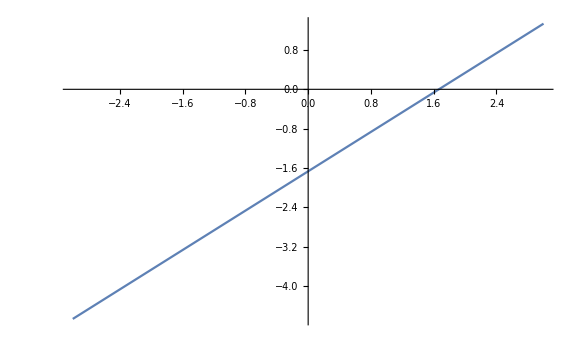

```mathematica
{t1=1.2,t2=1.0,gam=4/3,t3=0.0};
xleftPoint[t1_]:=Min@Map[(t1+t2 Cos[#]-gam/2)&,Range[0,2Pi,0.1]](*x轴方向投影最小*)
zeroPoint=Position[Map[xleftPoint[#]&,Range[-3,3,0.1]],#≥-0.1&&#≤0.1&]
Plot[xleftPoint[t1],{t1,-3,3},ImageSize->Large]
```

## 交集

```mathematica
{t1=1.,t2=1.0,gam=4/3,t3=0.0};
nonHermitian=ParametricPlot[{{t1+t2 Cos[k]-gam/2,t2 Sin[k]},{t1+t2 Cos[k]+gam/2,-t2 Sin[k]}},{k,0,2Pi},PlotTheme->"Scientific",FrameStyle->Directive[24,Bold],PlotStyle->{Blue,Purple},PlotRange->{{-1,3},{-2,2}}]
```

-Graphics-

## 手性螺旋

```mathematica
shift=1.0;
o1=Graphics3D[{Thick,Line[{{0,0,0},{0,0,2}}]}];
o2=Graphics3D[{Thick,Line[{{0,shift,0},{0,shift,2}}],Line[{{0,-shift,0},{0,-shift,2}}]}];
com1=ParametricPlot3D[{{Sin[u],Cos[u],u/10},{Sin[u],-Cos[u],u/10}},{u,0,20},PlotStyle->{Blue,Directive[Red,Dashed]},PlotTheme->"Scientific",AxesStyle->Directive[Orange, 24]];
Show[{com1,o1}]
com2=ParametricPlot3D[{{Sin[u],Cos[u]+shift,u/10},{Sin[u],-Cos[u]-shift,u/10}},{u,0,20},PlotStyle->{Blue,Directive[Red,Dashed]},PlotTheme->"Scientific",AxesStyle->Directive[Orange, 24]];
Show[{com2,o2}]
```

-Graphics3D-

-Graphics3D-